# Notes (MATH152, 2017-09-06)

Quiz: 6.3, 6.4, 6.6.

Sector area: θ/(2π)πr^2=θ/2 r^2, which for an angle in the unit circle, is θ/2.

```mathematica
Plot[x^2-y^2=1,{x,0
```

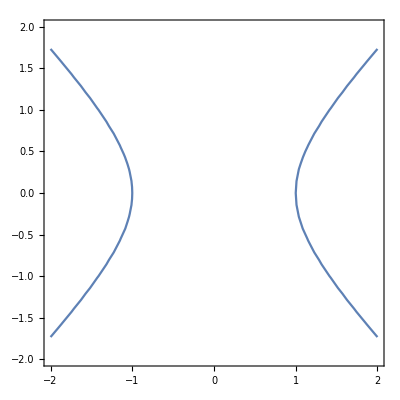

```mathematica
ContourPlot[x^2-y^2==1,{x,-2,2},{y,-2,2}]
```

## Hyperbolic trigonometric functions

```mathematica
sinh x = (e^x-e^-x)/2
cosh x=(e^x+e^-x)/2
tanh x=(sinh x)/(cosh x)
sech x=1/(cosh x)
csch x = 1/(sinh x)
coth x=(cosh x)/(sinh x)
```

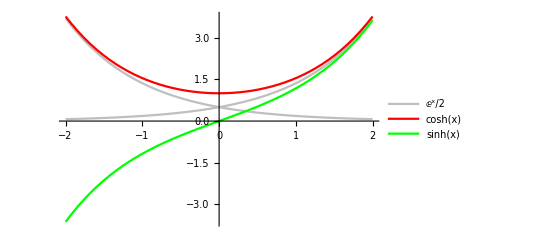

```mathematica
Plot[{E^x/2,E^-x/2,Cosh[x],Sin[x]},{x,-2,+2},PlotStyle->{GrayLevel[0.75], Dashed, Red, Green},PlotLegends->"Expressions"]
```

cosh(x) is a ‘catenary’ — the shape of a hanging string

### Domain & Range:

```mathematica
sinh x:ℝ->ℝ
```

```mathematica
cosh x:ℝ->[1,∞)
```

```mathematica
tanh x:ℝ->[-1,1]
```

### Identities:

```mathematica
sinh(-x)=(e^-x-e^x)/2=(-(e^x-e^-x))/2=-sinh(x)
```

```mathematica
cosh(-x)=(e^-x+e^x)/2=(e^x+e^-x)/2=cosh(x)
```

```mathematica
1-tanh^2 x=sech^2 x
```

```mathematica
sinh(x+y)=sinh x cosh y+cosh x sinh y
```

```mathematica
cosh(x+y)=cosh x cosh y+sinh x sinh y
```

```mathematica
cosh^2 x-sinh^2 x=1
```

```mathematica
Cosh[x]^2-Sinh[x]^2=((E^x+E^-x)/2)^2-((E^x-E^-x)/2)^2=((E^x+E^-x)^2)/4-((E^x-E^-x)^2)/4=(E^(2x)+2+E^(-2x))/4-(E^(2x)-2+E^(-2x))/4=2/4--2/4=1
```

```mathematica
ⅆ/ⅆx Sinh[x]=ⅆ/ⅆx 1/2(E^x-E^-x)=1/2(ⅆ/ⅆx E^x-ⅆ/ⅆx E^-x)=1/2(E^x-(-E^-x))=(E^x+E^-x)/2=Cosh[x]
```

(Derivation, or any other ‘differential operator’, are “linear” operators: you can always take coefficients out, and you can always distribute over summation)

```mathematica
ⅆ/ⅆx Cosh[x]=Sinh[x]
```

```mathematica
ⅆ/ⅆx Tanh[x]=ⅆ/ⅆx Sinh[x] Cosh[x]^-1=Cosh[x] Cosh[x]^-1-(Sinh^2)[x] Cosh[x]^-2=1-((Sinh^2)[x])/((Cosh^2)[x])=1-(Tanh^2)[x]=Sech[x]
```

```mathematica
ⅆ/ⅆx Sech[x]=-Sech[x]Tanh[x]
```

```mathematica
ⅆ/ⅆx Csch[x]=-Csch[x]Coth[x]
```

```mathematica
ⅆ/ⅆx Coth[x]=-(Csch^2)[x]
```

```mathematica
y=sinh^-1 x⇔x=sinh y
x=(e^y-e^-y)/2⇒e^y-2x-e^-y=0⇒e^(2y)-2x e^y-1=0
⟹^(z=e^y)z^2-2x z-1=0
z=(2x±√(4 x^2+4))/2=x±√(x^2+1)=e^y
```

Now, since x … something? we can get rid of the negative?

```mathematica
y=sinh^-1 x=ln(x+√(x^2+1)) ,x∈ℝ
cosh^-1 x=ln(x+√(x^2-1)),x≤1
tan^-1 x=1/2 ln((1+x)/(1-x))
```